## Neural networks - Part II

In part I, we have seen how to build very simple ANNs and how to extract information form ANNs. We also saw how to use Classify and Predict functions to automatically build and train ANNs for classification and prediction problems.

The aims of this part are:

To introduce the structure of data for ANNs: Tensors, net encoders, net decoders

To explore some pre-trained models.

To evaluate the accuracy of trained ANNs using test data.

To describe net surgery and give an example where net surgery is applied (in a separate notebook, Ch8-3_ML_NeuralNetworks_NetSurgery.nb .

## Network data - Encoders and decoders

### Tensors

Neural net layers operate on arrays (or tensors). 

In Mathematica, tensors can be thought as nested lists

Rank 0 (scalars): 1 (In practice, scalars are represented as length-1 vectors.)

Rank 1 (vectors): {1,2,3}

Vectors (1-tensors) representing elements of classes (categorical variables).

"a"  ≈ (1 | 0 | 0)
"b"  ≈ (0 | 1 | 0)
"c"  ≈ (0 | 0 | 1)

```mathematica
{0.7,0.3,0}
```

Rank 2 (matrices): {{1,2,3},{4,5,6}}

Matrix (2-tensor) representing a grayscale image.

-Graphics-  ≈ (0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0)

Rank n (n-tensors): {⋯{⋯{1,2,3}⋯}⋯}

3-tensor representing a color image.

-Graphics-  ≈ ((1 | 0 | 0
1 | 0 | 0
1 | 1 | 0) | (0 | 0 | 0
0 | 1 | 0
0 | 0 | 0) | (0 | 1 | 1
0 | 0 | 1
0 | 0 | 1))

The rank of a tensor corresponds to the output of the ArrayDepth function.

```mathematica
ArrayDepth[1]
```

0

```mathematica
ArrayDepth[{{1,2,3},{4,5,6}}]
```

2

### Encoding data

In the simple ANNs presented before for linear or logistic regression, the input and output were real numbers, i.e. they were scalars that can be readily be used by neural nets. 

In many cases, however, we wish to train and use ANNs on data such as images, audio, text, etc that do not have a tensor format. In order to use these data for ANNs, we need to translate it to an array of numeric values. This can be achieved with NetEncoderpaclet:ref/NetEncoder.

#### Encoder for two string classes

If we have several classes, e.g. “female” and “male”, we can assign an integer code to each class using the encoder “Class”:

```mathematica
enc=NetEncoder[{"Class",{"female","male"}}]
```

NetEncoder[<>]

Apply the encoder to an input:

```mathematica
enc["female"]
```

1

The encoder maps across a batch of inputs:

```mathematica
enc[{"male","female","female"}]
```

{2,1,1}

#### Encoding strings

Encoder that converts characters in an ASCII string to a sequence of integer codes

```mathematica
strenc=NetEncoder["Characters"]
```

NetEncoder[<>]

```mathematica
strenc["I enjoy neural networks"]
```

{44,3,72,81,77,82,92,3,81,72,88,85,68,79,3,81,72,87,90,82,85,78,86}

#### Encoding images

Create an image NetEncoderpaclet:ref/NetEncoder that produces a 1×12×12 array:

```mathematica
imageenc=NetEncoder[{"Image",{12,12},"ColorSpace"->"Grayscale"}]
```

NetEncoder[<>]

Take a 1x28x28 image and transform it to a 1x12x12 image using imageenc. 

Let us explore the image a bit first:

```mathematica
Information[-Graphics-]
```

Image

```mathematica
ImageData[-Graphics-]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,1},{1,1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1},{1,1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1},{1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,1,1,1,1},{1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1},{1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

We now apply the encoder:

```mathematica
imageenc[-Graphics-]//Normal
```

{{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,0.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,1.,1.},{1.,1.,0.,1.,1.,1.,1.,1.,0.,0.,1.,1.},{1.,1.,0.,0.,1.,1.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

In the encoded object, 0 is white and 1 is black.

The encoded image looks like a blurry “3”:

```mathematica
Image[imageenc[-Graphics-][[1]]]
```

-Graphics-

The image encoder conforms the image to have the specified colorspace, dimensions, etc. before it is converted to an array.

Apply the image NetEncoderpaclet:ref/NetEncoder on a large color image.

We first explore the image a bit:

```mathematica
img=-Graphics-;
ImageDimensions[img]
```

{150,155}

We can look at the colours for pixels along a horizontal cut of the image:

```mathematica
Table[RGBColor[ImageData[img][[75,i]]],{i,1,150}]
```

{RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 0.996078431372549}],RGBColor[{1., 1., 0.9568627450980393}],RGBColor[{1., 1., 1.}],RGBColor[{0.9372549019607843, 0.9215686274509803, 0.7058823529411765}],RGBColor[{0.7725490196078432, 0.7254901960784313, 0.18823529411764706}],RGBColor[{0.8, 0.6784313725490196, 0.19607843137254902}],RGBColor[{0.8313725490196079, 0.7568627450980392, 0.40784313725490196}],RGBColor[{0.9019607843137255, 0.8862745098039215, 0.7647058823529411}],RGBColor[{0.9058823529411765, 0.8588235294117647, 0.9803921568627451}],RGBColor[{0.8705882352941177, 0.8117647058823529, 0.7725490196078432}],RGBColor[{0.8509803921568627, 0.7725490196078432, 0.5686274509803921}],RGBColor[{0.9372549019607843, 0.8627450980392157, 0.7568627450980392}],RGBColor[{0.9254901960784314, 0.8823529411764706, 0.6862745098039216}],RGBColor[{0.8509803921568627, 0.7803921568627451, 0.25882352941176473}],RGBColor[{0.8666666666666667, 0.6862745098039216, 0.00392156862745098}],RGBColor[{0.8862745098039215, 0.6941176470588235, 0.}],RGBColor[{0.8745098039215686, 0.7372549019607844, 0.047058823529411764}],RGBColor[{0.8941176470588236, 0.7254901960784313, 0.08235294117647059}],RGBColor[{0.9215686274509803, 0.6235294117647059, 0.3411764705882353}],RGBColor[{0.9294117647058824, 0.615686274509804, 0.5764705882352941}],RGBColor[{0.9529411764705882, 0.6470588235294118, 0.2627450980392157}],RGBColor[{0.984313725490196, 0.6196078431372549, 0.}],RGBColor[{0.9882352941176471, 0.6196078431372549, 0.}],RGBColor[{0.9882352941176471, 0.615686274509804, 0.011764705882352941}],RGBColor[{0.9764705882352941, 0.611764705882353, 0.0196078431372549}],RGBColor[{0.9764705882352941, 0.6549019607843137, 0.06666666666666667}],RGBColor[{0.984313725490196, 0.6509803921568628, 0.10980392156862745}],RGBColor[{0.9803921568627451, 0.615686274509804, 0.3137254901960784}],RGBColor[{0.9019607843137255, 0.615686274509804, 0.5058823529411764}],RGBColor[{0.9137254901960784, 0.7450980392156863, 0.6}],RGBColor[{0.9411764705882353, 0.7725490196078432, 0.35294117647058826}],RGBColor[{0.9686274509803922, 0.596078431372549, 0.2901960784313726}],RGBColor[{0.9490196078431372, 0.596078431372549, 0.28627450980392155}],RGBColor[{0.9490196078431372, 0.611764705882353, 0.22745098039215686}],RGBColor[{0.9686274509803922, 0.5607843137254902, 0.23921568627450981}],RGBColor[{0.8549019607843137, 0.6078431372549019, 0.41568627450980394}],RGBColor[{0.8431372549019608, 0.5607843137254902, 0.37254901960784315}],RGBColor[{0.9450980392156862, 0.4588235294117647, 0.11764705882352941}],RGBColor[{0.9411764705882353, 0.49019607843137253, 0.17254901960784313}],RGBColor[{0.9333333333333333, 0.6078431372549019, 0.3333333333333333}],RGBColor[{0.9764705882352941, 0.6666666666666666, 0.3843137254901961}],RGBColor[{0.9490196078431372, 0.4392156862745098, 0.12549019607843137}],RGBColor[{0.9294117647058824, 0.34509803921568627, 0.16862745098039217}],RGBColor[{0.9254901960784314, 0.6196078431372549, 0.5137254901960784}],RGBColor[{0.8313725490196079, 0.47843137254901963, 0.3686274509803922}],RGBColor[{0.8509803921568627, 0.6509803921568628, 0.5686274509803921}],RGBColor[{0.9607843137254902, 0.8235294117647058, 0.7568627450980392}],RGBColor[{0.8313725490196079, 0.592156862745098, 0.5019607843137255}],RGBColor[{0.8509803921568627, 0.6509803921568628, 0.4}],RGBColor[{0.8509803921568627, 0.7333333333333333, 0.4235294117647059}],RGBColor[{0.8980392156862745, 0.7098039215686275, 0.5411764705882353}],RGBColor[{0.9686274509803922, 0.7333333333333333, 0.3764705882352941}],RGBColor[{0.9921568627450981, 0.7215686274509804, 0.28627450980392155}],RGBColor[{0.9647058823529412, 0.796078431372549, 0.49019607843137253}],RGBColor[{0.9490196078431372, 0.8901960784313725, 0.7843137254901961}],RGBColor[{0.7686274509803922, 0.6784313725490196, 0.7803921568627451}],RGBColor[{0.7176470588235294, 0.5254901960784314, 0.6549019607843137}],RGBColor[{0.8196078431372549, 0.5019607843137255, 0.43529411764705883}],RGBColor[{0.8901960784313725, 0.5254901960784314, 0.30196078431372547}],RGBColor[{0.9725490196078431, 0.788235294117647, 0.6431372549019608}],RGBColor[{0.9764705882352941, 0.7372549019607844, 0.43137254901960786}],RGBColor[{0.9764705882352941, 0.5568627450980392, 0.03137254901960784}],RGBColor[{0.9921568627450981, 0.5686274509803921, 0.023529411764705882}],RGBColor[{0.996078431372549, 0.5607843137254902, 0.}],RGBColor[{0.9803921568627451, 0.5450980392156862, 0.}],RGBColor[{0.9882352941176471, 0.6235294117647059, 0.058823529411764705}],RGBColor[{0.9803921568627451, 0.6862745098039216, 0.058823529411764705}],RGBColor[{0.984313725490196, 0.6901960784313725, 0.13725490196078433}],RGBColor[{0.9607843137254902, 0.7764705882352941, 0.43137254901960786}],RGBColor[{0.996078431372549, 0.9176470588235294, 0.6588235294117647}],RGBColor[{0.9764705882352941, 0.8509803921568627, 0.6235294117647059}],RGBColor[{0.8, 0.6862745098039216, 0.5686274509803921}],RGBColor[{0.8392156862745098, 0.7215686274509804, 0.43529411764705883}],RGBColor[{0.9764705882352941, 0.7843137254901961, 0.12941176470588237}],RGBColor[{0.9882352941176471, 0.8117647058823529, 0.09411764705882353}],RGBColor[{0.8705882352941177, 0.8156862745098039, 0.24313725490196078}],RGBColor[{0.7803921568627451, 0.7725490196078432, 0.4549019607843137}],RGBColor[{0.7058823529411765, 0.7529411764705882, 0.611764705882353}],RGBColor[{0.6862745098039216, 0.7686274509803922, 0.807843137254902}],RGBColor[{0.7176470588235294, 0.807843137254902, 0.9058823529411765}],RGBColor[{0.788235294117647, 0.8823529411764706, 0.9450980392156862}],RGBColor[{0.9176470588235294, 0.9215686274509803, 0.8392156862745098}],RGBColor[{1., 0.9568627450980393, 0.6666666666666666}],RGBColor[{0.9372549019607843, 0.9333333333333333, 0.8313725490196079}],RGBColor[{0.7019607843137254, 0.7803921568627451, 0.8588235294117647}],RGBColor[{0.7490196078431373, 0.8, 0.5254901960784314}],RGBColor[{0.9019607843137255, 0.8431372549019608, 0.17647058823529413}],RGBColor[{0.9725490196078431, 0.8705882352941177, 0.}],RGBColor[{0.984313725490196, 0.8862745098039215, 0.}],RGBColor[{1., 0.8862745098039215, 0.}],RGBColor[{1., 0.8823529411764706, 0.00784313725490196}],RGBColor[{1., 0.8901960784313725, 0.043137254901960784}],RGBColor[{0.9686274509803922, 0.8823529411764706, 0.1450980392156863}],RGBColor[{0.9294117647058824, 0.8901960784313725, 0.24705882352941178}],RGBColor[{0.9176470588235294, 0.8666666666666667, 0.42745098039215684}],RGBColor[{0.8784313725490196, 0.8196078431372549, 0.5529411764705883}],RGBColor[{0.9333333333333333, 0.9098039215686274, 0.7098039215686275}],RGBColor[{1., 1., 0.9568627450980393}],RGBColor[{1., 1., 1.}],RGBColor[{0.9882352941176471, 1., 0.9921568627450981}],RGBColor[{0.9764705882352941, 1., 0.9764705882352941}],RGBColor[{0.984313725490196, 1., 0.984313725490196}],RGBColor[{0.996078431372549, 1., 0.9882352941176471}],RGBColor[{1., 1., 0.9921568627450981}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}],RGBColor[{1., 1., 1.}]}

```mathematica
Image[{ImageData[img][[75]]}]
```

-Graphics-

```mathematica
ImageData[img][[1,1]]
```

{1.,1.,1.}

We now apply the encoder.

Once we apply the encoder, the dimensions of the encoded image change.

```mathematica
imageenc[img]//Dimensions
```

{1,12,12}

```mathematica
ie=imageenc[img]
```

{{{1.,1.,1.,1.,0.996078,1.,0.968627,0.996078,0.992157,1.,1.,1.},{1.,0.996078,0.964706,0.968627,1.,0.984314,0.866667,1.,1.,0.992157,1.,1.},{1.,1.,1.,0.866667,0.921569,0.894118,0.74902,0.890196,0.745098,0.87451,0.996078,0.992157},{0.992157,0.921569,0.909804,0.729412,0.819608,0.878431,0.65098,0.470588,0.603922,1.,1.,1.},{0.996078,0.933333,0.72549,0.635294,0.635294,0.713726,0.627451,0.596078,0.678431,0.858824,0.921569,0.968627},{1.,1.,0.878431,0.729412,0.635294,0.627451,0.705882,0.729412,0.772549,0.788235,0.921569,0.988235},{0.984314,0.854902,0.713726,0.772549,0.803922,0.72549,0.592157,0.698039,0.839216,0.937255,1.,1.},{0.964706,0.886275,0.870588,0.760784,0.819608,0.741176,0.556863,0.521569,0.682353,0.815686,0.945098,1.},{1.,1.,0.996078,0.603922,0.694118,0.760784,0.780392,0.698039,0.721569,0.933333,0.929412,0.992157},{0.996078,0.996078,0.92549,0.913725,0.929412,0.733333,0.913725,0.901961,0.858824,1.,1.,1.},{1.,1.,1.,1.,0.972549,0.847059,1.,1.,0.952941,0.984314,0.996078,1.},{1.,1.,1.,0.996078,0.996078,0.988235,1.,0.996078,1.,1.,1.,1.}}}

One can look at the image resulting from encoding. Each number in the encoded image is a level of grey (from 0: White to 1: Black).

```mathematica
Image[ie[[1]]]
```

-Graphics-

### Decoding data

In some cases, the outputs of neural nets are numerical predictions that do not require decoding. 

In many cases, however, we would like to convert numerical arrays to human readable classes, images, audio, etc.

#### Decoding to classes

For example, the output of an ANN could give the probability that the gender of a face corresponds to male or female

```mathematica
dec=NetDecoder[{"Class",{"male","female"}}]
```

NetDecoder[<>]

```mathematica
dec[{1,2}]
```

female

```mathematica
dec[{2,1}]
```

male

```mathematica
dec[{0.51,0.5}]
```

male

#### Decoding to images

```mathematica
imagedec=NetDecoder[{"Image","ColorSpace"->"Grayscale"}]
```

NetDecoder[<>]

```mathematica
imagedec[imageenc[-Graphics-]]
```

-Graphics-

```mathematica
imagedec[imageenc[img]]
```

-Graphics-

## Pre-trained Neural Networks

The Wolfram Neural Net Repository is a public resource that hosts an expanding collection of trained and untrained neural network models suitable for immediate evaluation, training, visualization, transfer learning and more. 

In this section, we will

Focus a bit on a classic: An ANN to identify images of handwritten images.

Give two more examples: Facial features and a machine trained to paint as Cezanne (really?).

Feel free to explore the Wolfram Neural Net Repository to find many interesting ANNs.

### LeNet Trained on MNIST Data - Identify the handwritten digit in an image

This pioneer work for image classification with convolutional neural nets was released in 1998. It was developed by Yann LeCun and his collaborators at AT&T Labs while they experimented with a large range of machine learning solutions for classification on the MNIST dataset.

It is a classic in machine learning.

Training data: MNIST Database of Handwritten Digits, consisting of 60,000 training and 10,000 test grayscale images of size 28x28.

```mathematica
28 28
```

784

#### The data

The MNIST dataset is available from the Wolfram Data Repository:

```mathematica
trainingData=ResourceData["MNIST","TrainingData"];
testData=ResourceData["MNIST","TestData"];
```

Useful to see some examples from the data:

```mathematica
RandomSample[trainingData,10]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→0,-Graphics-→5,-Graphics-→1,-Graphics-→3,-Graphics-→7,-Graphics-→4,-Graphics-→7,-Graphics-→7}

```mathematica
Keys[%]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
%[[1]]
```

-Graphics-

```mathematica
Information[-Graphics-]
```

Image

#### The trained LeNet model

We can obtain a pre-trained version of LeNet from the Wolfram Neural Net Repository:

```mathematica
lenetModel=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

#### Evaluating the performance of the model

The pre-trained model can be readily used for classification of handwritten digits.

Trying this on a random sample of the test dataset suggests a good accuracy:

```mathematica
randTest=RandomSample[testData,10]
```

{-Graphics-→3,-Graphics-→1,-Graphics-→3,-Graphics-→3,-Graphics-→1,-Graphics-→5,-Graphics-→7,-Graphics-→6,-Graphics-→1,-Graphics-→2}

```mathematica
Keys[randTest]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lenetModel[Keys[randTest]]
```

{3,1,3,3,1,5,7,6,1,2}

```mathematica
lenetModel[Keys[randTest],"Probabilities"]
```

{<|0→8.18564×10^-24,1→9.51247×10^-18,2→9.25403×10^-15,3→1.,4→1.28306×10^-18,5→3.27534×10^-11,6→2.28983×10^-19,7→1.66295×10^-12,8→4.4747×10^-13,9→3.42826×10^-15|>,<|0→1.05653×10^-7,1→0.999578,2→3.53995×10^-6,3→0.0000790935,4→4.68305×10^-6,5→0.0000889204,6→2.54187×10^-7,7→0.000208215,8→2.40409×10^-6,9→0.0000348947|>,<|0→2.00521×10^-17,1→5.29932×10^-14,2→4.70996×10^-14,3→1.,4→4.9966×10^-21,5→1.47513×10^-8,6→1.06946×10^-14,7→2.7216×10^-17,8→4.96397×10^-12,9→4.89669×10^-20|>,<|0→2.92061×10^-16,1→1.0997×10^-16,2→2.92008×10^-15,3→1.,4→3.8064×10^-26,5→4.51163×10^-10,6→1.96176×10^-17,7→1.30977×10^-15,8→6.08387×10^-14,9→9.48139×10^-19|>,<|0→1.77081×10^-12,1→1.,2→5.1303×10^-11,3→2.09404×10^-10,4→8.21432×10^-8,5→3.33267×10^-9,6→2.54406×10^-10,7→5.66092×10^-10,8→2.04335×10^-8,9→7.9817×10^-9|>,<|0→2.04121×10^-12,1→3.30033×10^-12,2→1.32199×10^-9,3→6.60943×10^-8,4→4.01561×10^-12,5→0.99996,6→2.98187×10^-11,7→1.12586×10^-11,8→3.92553×10^-6,9→0.0000355078|>,<|0→8.02861×10^-11,1→1.60116×10^-6,2→3.35158×10^-7,3→3.17061×10^-8,4→2.2267×10^-7,5→2.09589×10^-8,6→1.0128×10^-14,7→0.999943,8→0.0000343727,9→0.0000207575|>,<|0→2.46919×10^-13,1→1.75196×10^-15,2→1.1993×10^-11,3→4.51881×10^-13,4→1.3034×10^-11,5→1.55259×10^-7,6→1.,7→1.19907×10^-20,8→3.29868×10^-12,9→1.56203×10^-20|>,<|0→8.28776×10^-13,1→1.,2→8.92612×10^-11,3→1.49857×10^-10,4→7.15151×10^-8,5→6.26389×10^-9,6→2.91909×10^-10,7→3.97771×10^-9,8→3.89248×10^-10,9→3.0027×10^-9|>,<|0→6.13381×10^-16,1→1.88947×10^-18,2→1.,3→9.55662×10^-20,4→1.40311×10^-25,5→5.55779×10^-27,6→3.17454×10^-27,7→1.31994×10^-16,8→2.11575×10^-17,9→6.93257×10^-29|>}

One can test the performance in a similar way as done for classifiers and predictors trained with Classify and Predict.

```mathematica
cm=ClassifierMeasurements[lenetModel,testData]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.9848

Obtain a list of examples for which the loss was the highest:

```mathematica
cm["WorstClassifiedExamples"]
```

{-Graphics-→6,-Graphics-→6,-Graphics-→2,-Graphics-→8,-Graphics-→5,-Graphics-→6,-Graphics-→6,-Graphics-→0,-Graphics-→1,-Graphics-→8}

```mathematica
Keys[cm["WorstClassifiedExamples"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lenetModel[Keys[cm["WorstClassifiedExamples"]]]
```

{4,0,7,9,9,0,0,8,7,7}

To which “wrong” class are the worst classified examples attributed with highest probability?

```mathematica
lenetModel[Keys[cm["WorstClassifiedExamples"]],"TopProbabilities"]
```

{{4→1.},{0→0.999602},{7→0.999699},{9→0.999822},{9→0.999893},{0→0.999995},{0→0.999994},{8→0.999782},{7→0.999974},{7→0.999532}}

These examples are classified to a wrong class with high confidence (this is a bad as it can get in terms of classification...). Fortunately, most examples in the training dataset are properly classified as shown by the high value of the the accuracy.

We can have a look at the probability that any of these examples are classified to each of the classes:

```mathematica
lenetModel[Keys[cm["WorstClassifiedExamples"]],"Probabilities"]
```

{<|0→1.01524×10^-19,1→3.13288×10^-16,2→1.67527×10^-10,3→4.10983×10^-18,4→1.,5→7.87142×10^-14,6→1.37793×10^-10,7→2.55915×10^-15,8→5.51619×10^-9,9→1.27471×10^-13|>,<|0→0.999602,1→1.53184×10^-13,2→6.03372×10^-7,3→2.88661×10^-9,4→2.65085×10^-8,5→4.97034×10^-6,6→1.82878×10^-7,7→2.25749×10^-11,8→5.62412×10^-6,9→0.000386723|>,<|0→3.80175×10^-14,1→2.27839×10^-8,2→3.02987×10^-7,3→1.85844×10^-7,4→6.00511×10^-6,5→1.7151×10^-10,6→1.56214×10^-18,7→0.999699,8→0.0000206979,9→0.000274002|>,<|0→7.01152×10^-13,1→1.26039×10^-9,2→2.31236×10^-6,3→1.32274×10^-7,4→0.00017065,5→9.40246×10^-7,6→6.32252×10^-14,7→9.97289×10^-8,8→3.59741×10^-6,9→0.999822|>,<|0→1.37431×10^-15,1→1.49244×10^-12,2→2.79822×10^-11,3→0.000100474,4→2.14418×10^-6,5→3.83048×10^-6,6→1.55825×10^-15,7→1.19643×10^-12,8→3.01819×10^-7,9→0.999893|>,<|0→0.999995,1→6.38725×10^-15,2→1.08215×10^-11,3→3.10204×10^-10,4→5.16417×10^-7,5→1.03544×10^-8,6→4.49197×10^-6,7→2.89941×10^-13,8→3.33868×10^-12,9→1.12545×10^-9|>,<|0→0.999994,1→2.12949×10^-20,2→6.07715×10^-10,3→1.52896×10^-13,4→4.7641×10^-15,5→1.71478×10^-9,6→6.01486×10^-6,7→2.22634×10^-17,8→2.82851×10^-8,9→8.21605×10^-12|>,<|0→6.04308×10^-6,1→0.000101478,2→4.52401×10^-8,3→5.20155×10^-15,4→4.22049×10^-11,5→0.000107344,6→2.886×10^-6,7→1.097×10^-12,8→0.999782,9→1.70319×10^-9|>,<|0→2.49465×10^-9,1→0.0000245374,2→6.02999×10^-10,3→8.4524×10^-11,4→7.8934×10^-10,5→2.33925×10^-10,6→1.81766×10^-14,7→0.999974,8→1.37113×10^-8,9→9.80135×10^-7|>,<|0→3.58027×10^-13,1→3.78337×10^-6,2→2.19871×10^-7,3→2.75721×10^-8,4→0.0000195986,5→8.79993×10^-10,6→2.0368×10^-17,7→0.999532,8→0.000026556,9→0.000417421|>}

Obtain a list of examples for which the net was least certain of the class (i.e. no high probability to be assigned to a unique class):

```mathematica
cm["LeastCertainExamples"]
```

{-Graphics-→6,-Graphics-→2,-Graphics-→9,-Graphics-→6,-Graphics-→6,-Graphics-→7,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→6}

```mathematica
lenetModel[Keys[cm["LeastCertainExamples"]]]
```

{6,2,9,1,6,7,8,2,4,6}

```mathematica
lenetModel[Keys[cm["LeastCertainExamples"]],"TopProbabilities"]
```

{{6→0.242531,5→0.167526,0→0.160988,9→0.123339,4→0.1118,8→0.105095,1→0.0764827},{2→0.339246,3→0.307557,0→0.120168,9→0.11314,5→0.0815516},{9→0.495518,7→0.164678,3→0.123249,5→0.0923205,1→0.077099},{1→0.419449,6→0.279902,4→0.147505,5→0.103918},{6→0.382837,5→0.349125,1→0.188268},{7→0.480127,9→0.296099,8→0.0756276,4→0.0691457},{8→0.499543,2→0.331192,9→0.0740492,3→0.0524996},{2→0.406111,8→0.318856,0→0.255175},{4→0.613338,7→0.24288},{6→0.478651,5→0.395749,8→0.066747,9→0.0571849}}

What are the classification probabilities for these?

```mathematica
lenetModel[Keys[cm["LeastCertainExamples"]],"Probabilities"]
```

{<|0→0.160988,1→0.0764827,2→0.00446181,3→0.0019394,4→0.1118,5→0.167526,6→0.242531,7→0.00583646,8→0.105095,9→0.123339|>,<|0→0.120168,1→0.0000226779,2→0.339246,3→0.307557,4→0.0107386,5→0.0815516,6→1.25761×10^-8,7→0.0253869,8→0.00218847,9→0.11314|>,<|0→0.000672657,1→0.077099,2→0.0015105,3→0.123249,4→0.0417314,5→0.0923205,6→0.0000422481,7→0.164678,8→0.0031788,9→0.495518|>,<|0→0.000436235,1→0.419449,2→0.00465187,3→0.00150393,4→0.147505,5→0.103918,6→0.279902,7→0.000626398,8→0.0387753,9→0.00323243|>,<|0→0.00297925,1→0.188268,2→0.0186456,3→0.0178104,4→0.0321836,5→0.349125,6→0.382837,7→0.000280537,8→0.00739182,9→0.000478534|>,<|0→0.000783599,1→0.00221728,2→0.0479325,3→0.027149,4→0.0691457,5→0.00090622,6→0.0000117266,7→0.480127,8→0.0756276,9→0.296099|>,<|0→0.00309969,1→0.00273524,2→0.331192,3→0.0524996,4→0.000104037,5→0.004226,6→0.00494635,7→0.0276047,8→0.499543,9→0.0740492|>,<|0→0.255175,1→0.0000746443,2→0.406111,3→0.000571433,4→0.0000187339,5→0.0000107597,6→0.0000203197,7→0.0187334,8→0.318856,9→0.000428063|>,<|0→0.0303404,1→0.0359093,2→0.0548082,3→0.00328436,4→0.613338,5→0.00472029,6→0.00342663,7→0.24288,8→0.00385272,9→0.00744027|>,<|0→0.00166327,1→1.17299×10^-11,2→1.29537×10^-7,3→4.43064×10^-9,4→4.96862×10^-6,5→0.395749,6→0.478651,7→4.09258×10^-11,8→0.066747,9→0.0571849|>}

We can also use NetMeasurementspaclet:ref/NetMeasurements to measure various properties of the net. It shares many properties with ClassifierMeasurementspaclet:ref/ClassifierMeasurements but each has properties of its own. 

NetMeasurementspaclet:ref/NetMeasurements has the advantage that it is efficiently implemented for networks and can be run on GPU.

The syntax for NetMeasurements is:

NetMeasurements[net,testdata,”measurement”]

```mathematica
NetMeasurements[lenetModel,testData,"Accuracy"]
```

0.9848

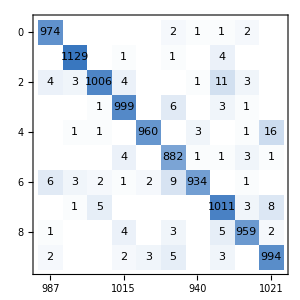
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[lenetModel,testData,"ConfusionMatrixPlot"]
```

```mathematica
N[974/980]
```

0.993878

```mathematica
TPR=NetMeasurements[lenetModel,testData,"TruePositiveRate"]
```

<|0→0.993878,1→0.994714,2→0.974806,3→0.989109,4→0.977597,5→0.988789,6→0.974948,7→0.983463,8→0.9846,9→0.985134|>

#### Comparing to other classification methods

In order to compare LeNet with other classification methods, we can use Classify to automatically train an effective classifier:

```mathematica
classifier=Classify[trainingData,ValidationSet->testData]
```

ClassifierFunction[…]

```mathematica
cmOther=ClassifierMeasurements[classifier,testData]
```

ClassifierMeasurementsObject[…]

```mathematica
cmOther["Accuracy"]
```

0.897

In general, LeNet outperforms the accuracy of classifier no matter the method used.

#### Training the LeNet model

The LeNet model is already trained but it is easy to train it. Here,

```mathematica
NetTrain[NetModel["LeNet"],trainingData,ValidationSet->testData]
```

NetChain[<>]

#### Layers in LeNet

Let us explore the layers of LeNet:

```mathematica
lenetModel
```

NetChain[<>]

```mathematica
Information[lenetModel,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysLearningRateMultipliers,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
Information[lenetModel,"SummaryGraphic"]
```

-Graphics-

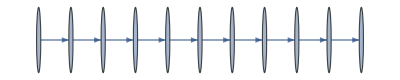

```mathematica
Information[lenetModel,"LayersGraph"]
```

The net is composed of a variety of layers, such as a ConvolutionLayerpaclet:ref/ConvolutionLayer, PoolingLayerpaclet:ref/PoolingLayer, etc. Each of these layers accomplishes different tasks, in this case, tasks related to computer vision.

Take a look at the last layer of the net.

Extract the last layer of the net using NetExtractpaclet:ref/NetExtract:

```mathematica
layer=NetExtract[lenetModel,-1]
```

SoftmaxLayer[<>]

Like any layer, we can apply this layer to an input to get an output:

```mathematica
layer[{1,2,5,2,4,7,4,3,5,3}]
```

{0.00174213,0.00473559,0.0951169,0.00473559,0.0349916,0.702824,0.0349916,0.0128727,0.0951169,0.0128727}

A layer can also accept a NumericArraypaclet:ref/NumericArray input, yielding a NumericArraypaclet:ref/NumericArray in this case:

```mathematica
layer[NumericArray[…]]
```

NumericArray[…]

```mathematica
Normal[%]
```

{0.00174213,0.00473559,0.0951169,0.00473559,0.0349916,0.702824,0.0349916,0.0128727,0.0951169,0.0128727}

The purpose of a SoftmaxLayerpaclet:ref/SoftmaxLayer is to produce probabilities that sum to 1.

Sum up the previous output:

```mathematica
Total[%]
```

1.

### Identifying facial features

Determine the locations of the eyes, nose and mouth from a facial image

```mathematica
img = -Graphics-;
```

Get the pre-trained Vanilla CNN for Facial Landmark Regression model:

```mathematica
net=NetModel["Vanilla CNN for Facial Landmark Regression"]
```

NetChain[<>]

Get the locations of the eyes, nose and mouth corners:

```mathematica
landmarks=net[img]
```

{{0.314553,0.639713},{0.723497,0.64065},{0.498151,0.398069},{0.35471,0.169666},{0.677748,0.173031}}

```mathematica
HighlightImage[img,{PointSize[0.04],Normal[landmarks]},DataRange->{{0,1},{0,1}}]
```

-Graphics-

### Turn a photo into a Cezanne-style painting

```mathematica
cezanne=NetModel["CycleGAN Photo-to-Cezanne Translation"]
```

NetChain[<>]

```mathematica
NetModel["CycleGAN Photo-to-Cezanne Translation"][-Graphics-]
```

```mathematica
Information[cezanne,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysLearningRateMultipliers,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

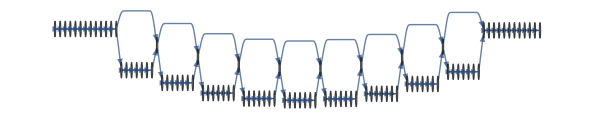

```mathematica
Information[cezanne,"LayersGraph"]
```

```mathematica
Information[cezanne,"FullSummaryGraphic"]
```

-Graphics-